```mathematica
ClearAll["Global`*"]
```

```mathematica
n=9;
grid1=Table[((i-1.)/(n-1.))^2,{i,1,n,1}];
grid2=Table[(i-1.)/(n-1.),{i,1,n,1}];
dp1=Table[grid1[[i+1]]-grid1[[i]],{i,1,n-1}];
ccells1 = Table[0.5*(grid1[[i+1]]+grid1[[i]]),{i,1,n-1}];
tfunc1 = Exp[ccells1]*dp1;
totmass =Flatten[{0,Table[Total[tfunc1[[1;;i]]],{i,1,n-1}]}];
```

```mathematica
D[InterpolatingPolynomial[Transpose[{grid1[[1;;5]],totmass[[1;;5]]}],x],{x,1}]
```

```mathematica
handinterp[x_]:=Sum[totmass[[k]]*Product[(x-grid1[[l]])/(grid1[[k]]-grid1[[l]]),{l,n-4,k-1}]*Product[(x-grid1[[l]])/(grid1[[k]]-grid1[[l]]),{l,k+1,n}],{k,n-4,n,1}]
handinterpd[x_]:=Sum[totmass[[k]]*
(Sum[1/(x-grid1[[l]]),{l,n-4,k-1}]+Sum[1/(x-grid1[[l]]),{l,k+1,n}])*(Product[(x-grid1[[l]])/(grid1[[k]]-grid1[[l]]),{l,n-4,k-1}]*Product[(x-grid1[[l]])/(grid1[[k]]-grid1[[l]]),{l,k+1,n}]),
{k,n-4,n}]
```

```mathematica
FullSimplify[handinterpd[x]]/.{x->0}
```

0.994004

```mathematica
grid1;
totmass
```

{0,0.0157475,0.0644898,0.150966,0.283933,0.477652,0.754461,1.14907,1.71571}

```mathematica
FullSimplify[D[InterpolatingPolynomial[Transpose[{grid1[[n-4;;n]],totmass[[n-4;;n]]}],x],{x,1}]]
```

0.991477+x (1.05765+(0.351016+0.312066 x) x)

```mathematica
D[Product[(x-a[l])/(a[k]-a[l]),{l,1,k-1}]*Product[(x-a[l])/(a[k]-a[l]),{l,k+1,m}],{x,1}]
```

(∂_x ∏_(l=1+k)^m (x-a[l])/(a[k]-a[l])) ∏_(l=1)^(-1+k) (x-a[l])/(a[k]-a[l])+(∂_x ∏_(l=1)^(-1+k) (x-a[l])/(a[k]-a[l])) ∏_(l=1+k)^m (x-a[l])/(a[k]-a[l])

```mathematica
A = Table[grid1[[i]]^j,{i,5,8,1},{j,4,0,-1}];
A[[1,5]]=1;
b=totmass[[5;;8]];
x=Inverse[A].b;
```

Power::indet: Indeterminate expression 0.^0 encountered.

```mathematica
4*x[[1]]*grid1[[9]]^3+3*x[[2]]*grid1[[9]]^2+2*x[[3]]*grid1[[9]]^1+1*x[[4]]
```

2.67485

```mathematica
2^14
```

16384

```mathematica
AList = {A12,A32,A52};
xList={x12,x32,x52};
poly[x_]:=InterpolatingPolynomial[Transpose[{xList,AList}],y]/.{y->x}
```

```mathematica
FullSimplify[D[poly[x],x]]
```

(A52 (2 x-x12-x32) (x12-x32)+A12 (2 x-x32-x52) (x32-x52)+A32 (-2 x x12+x12^2+2 x x52-x52^2))/((x12-x32) (x12-x52) (x32-x52))

```mathematica
D[Product[x-x[i],{i,1,3,1}],x]
```

(x-x[1]) (x-x[2])+(x-x[1]) (x-x[3])+(x-x[2]) (x-x[3])

```mathematica
ⅇ^0./ⅇ^1
```

0.367879

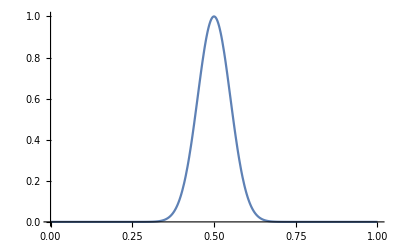

```mathematica
f[x_]:=ⅇ^(-1/2((x-0.5)/0.05)^2)
Plot[f[x],{x,0,1}, PlotRange->{0,1}]
```

```mathematica
f[0]
f[0.5]
f[1]
```

1.92875×10^-22

1.

1.92875×10^-22